# Mixed Postman Tour

## Created Wednesday July 13, 2022

This document contains a condensed set of instructions on how to solve the Mixed Chinese Postman Problem (MCPP), based on the algorithms described in Chapter 4 of Arc Routing: Problems, Methods, and Applications.

https://drive.google.com/file/d/12j-JQUZTTdeC4NXWyFFm3uODFLpAg2wJ/view

## Overview [[Incomplete]]

Our project goal is to implement an algorithm that takes a mixed graph (graph) and produces a list of edges that is an optimal postman tour through that graph. The existing FindPostmanTour function in Mathematica does not support mixed graphs:

FindPostmanTour::ngen: The generalized FindPostmanTour[Graph[<3>, <3>]] is not implemented.

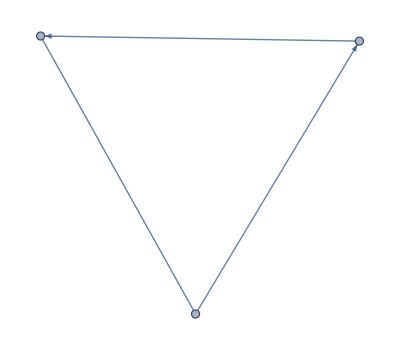
FindPostmanTour[-Graphics-]

```mathematica
FindPostmanTour[Graph[{1<->2,2->3,3->1}]]
```

Chapter 4 of Arc Routing describes a solution to the Mixed Chinese Postman Tour problem. That solution is described by the following points:

If a graph is Eulerian, then Arc Routing states that finding the single tour through that graph is easily computable.

If the graph is not Eulerian, chapter 4 contains

```mathematica
-Graphics--Graphics-
```

```mathematica
-Graphics--Graphics-
```

## Phase 1

## Notes on Book Notation

E — the set of undirected edges

A — the set of directed edges (arcs)

δ^+(S) — the set of directed edges (arcs) that start at S (and are not self loops)

δ^-(S) — the set of directed edges (arcs) that end at S (and are not self loops)

δ(S) — the set of undirected edges with exactly one endpoint at S

δ^*(S) — the union of δ(S), δ^-(S), and δ^+(S); i.e. all directed and undirected edges that start or end at S

x(F) — where F is a subset of edges, the sum of the number of times those links appear in the tour

Let x_e represent the number of times a link e ∈ E ∪ A appears in the tour.

## Implementation

### Install Peter’s paclet

```mathematica
PacletInstall["PeterBurbery/MixedGraphs"]
```

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

### Generate a random mixed graph using Peter’s RandomMixedGraph

```mathematica
ConnectedGraph[]:= Module[{g, edges},
    	g = RandomMixedGraph[{8, 10}, 0.4];
    	edges = EdgeList[g] //. n_Integer :> CharacterRange["A", "Z"][[n]];
    	g = Graph[edges, VertexLabels -> "Name"];
    	Print[ConnectedGraphQ[g]];
    	g
  ]
```

```mathematica
Remove[ConnectedGraph]
```

```mathematica
ConnectedGraph[]:=NestWh.ile[RandomMixedGraph[{8,10},0.4 ,VertexLabels->"Name"],Null,!ConnectedGraphQ[#]&]
```

```mathematica
ConnectedGraph[]
```

$Aborted

```mathematica
2+2
```

True

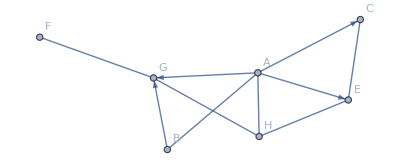

```mathematica
NestWhile[ConnectedGraph[]&,Null,!ConnectedGraphQ[#]&]
```

```mathematica
ConnectedGraphQ[-Graphics-]
```

True

```mathematica
PersistentSymbol["G","Local"]=G;
```

```mathematica
G=PersistentSymbol["G","Local"]
```

-Graphics-

```mathematica
G
```

-Graphics-

### FindMixedPostmanTour

#### Attempt by Connor

```mathematica
FindMixedPostmanTour[graph_?MixedGraphQ]:=Block[{
	n,
	dirEdges,
	undirCount, dirCount,

	undirDirA, (* Subscript[x, ij] ∈ E *)
	undirDirB, (* Subscript[x, ji] ∈ E *)
	directed       (* Subscript[x, ij] ∈ A *)
},
	undirCount=EdgeCount[graph,_UndirectedEdge];
	dirCount=EdgeCount[graph,_DirectedEdge];

	dirEdges=EdgeList[graph,_DirectedEdge];

	m=Transpose[IncidenceMatrix[Graph[dirEdges]]];
	a=UnitStep[m-1];
	b=a-m;

	Print[Dimensions[a]];

	res=LinearOptimization[
		-(Total[undirDirA+undirDirB]+Total[directed]),
		{
			(* 4.11 *)
			undirDirA+undirDirB\[VectorGreaterEqual]1,

			(* 4.12 *)
			(*a.u +b.v\[VectorLessEqual]1,
			a.v +b.u\[VectorLessEqual]1,*)
			a.directed+b.directed\[VectorLessEqual]1,

			(* 4.13 *)
			directed\[VectorGreaterEqual]1,

			(* 4.14 *)
			undirDirA\[VectorGreaterEqual]0,
			undirDirB \[VectorGreaterEqual] 0
		},
		{
			undirDirA∈Vectors[undirCount,Integers],
			undirDirB∈Vectors[undirCount,Integers],
			directed∈Vectors[dirCount,Integers]
		}
	];
]
```

```mathematica
FindMixedPostmanTour[G]
```

```mathematica
IncidenceMatrixDataset[G]
```

#### Jaebum’s Code

```mathematica
FindMixedPostmanTour[g_?GraphQ]:=Block[{
	une,de,
	unX,
	unrevX,
	dX,
	vlist,
	c412,
	elist,
	res,
	edges
},
	une=EdgeList[g,_UndirectedEdge];
	de=EdgeList[g,_DirectedEdge];

	unX=und@@@une;
	unrevX=Reverse/@unX;

	Print["unX: ", unX];

	dX=d@@@de;
	vlist=VertexList[g];
	c412=
		Total[
			Flatten[{Cases[dX, d[#,_]], -Cases[dX, d[_,#]]}]
		]+Total[
			Cases[unX, und[#,_]|und[_,#]]
			-Reverse/@Cases[unX, und[#,_]|und[_,#]]
		]&/@vlist;

	Print["c412: ", c412];

	elist=Flatten[{unX,unrevX,dX}];
	res=LinearOptimization[
		(Total[unX+unrevX]+Total[dX]),
		{
			(*4.11*)
			unX+unrevX\[VectorGreaterEqual]1,

			(*4.12*)(*a.u+b.v\[VectorLessEqual]1,a.v+b.u\[VectorLessEqual]1,*)
			c412==0,

			(*4.13*)
			dX\[VectorGreaterEqual]1,

			(*4.14*)
			unX\[VectorGreaterEqual]0,
			unrevX\[VectorGreaterEqual]0
		},
		Element[#,Integers]&/@elist
	];

	edges=Flatten[
		If[#[[2]]>0,Table[#[[1]],{#[[2]]}],Nothing]&/@res
	]/.{und->UndirectedEdge,d->DirectedEdge}
]
```

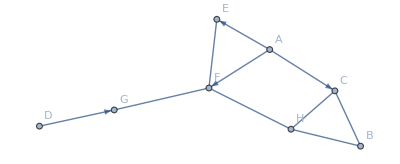

```mathematica
G
```

```mathematica
duplicateRevisitedEdges=FindMixedPostmanTour[-Graphics-]
```

unX: {und[A,B],und[A,H],und[C,E],und[E,H],und[F,G],und[G,H]}

c412: {d[A,C]+d[A,E]+d[A,G]+und[A,B]+und[A,H]-und[B,A]-und[H,A],-d[A,G]-d[B,G]+und[F,G]-und[G,F]+und[G,H]-und[H,G],-d[A,C]+und[C,E]-und[E,C],-d[A,E]+und[C,E]-und[E,C]+und[E,H]-und[H,E],d[B,G]+und[A,B]-und[B,A],und[A,H]+und[E,H]+und[G,H]-und[H,A]-und[H,E]-und[H,G],und[F,G]-und[G,F]}

{C<->E,E<->H,F<->G,G<->H,G<->H,B<->A,H<->A,H<->A,H<->E,G<->F,A->G,A->C,A->E,B->G}

```mathematica
?FindMixedPostmanTour
```

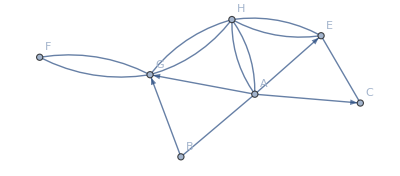

```mathematica
Graph[duplicateRevisitedEdges,VertexLabels->"Name"]
```

```mathematica
EulerianGraphQ[Graph[duplicateRevisitedEdges,VertexLabels->"Name"]]
```

EulerianGraphQ::ngen: The generalized EulerianGraphQ[Graph[<7>, <14>]] is not implemented.

EulerianGraphQ[-Graphics-]

FindEulerianCycle::ngen: The generalized FindEulerianCycle[Graph[<7>, <16>]] is not implemented.

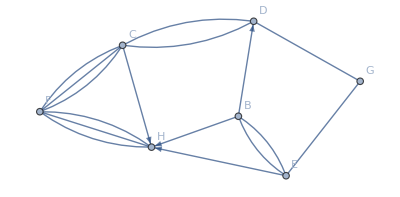
FindEulerianCycle[-Graphics-]

```mathematica
FindEulerianCycle[%71]
```

#### IncidenceMatrixDataset

```mathematica
IncidenceMatrixDataset[g_?GraphQ]:=Module[{},
	Association@Map[
		args|->args[[1]]->Association[
			Thread[Map[ToString,EdgeList[G]]->args[[2]]]
		],
		Transpose[{VertexList[G],m}]
	]//Dataset
]
```

```mathematica
IncidenceMatrixDataset[G]
```

Transpose::nmtx: The first two levels of {{A,G,C,E,B,H,F},m} cannot be transposed.

## Bug: VertexDegree on mixed graph with integer nodes is wrong

```mathematica
InputForm[G]
```

Graph[{1, 2, 3, 4, 5, 6, 7, 8}, {}, {FormatType -> TraditionalForm, 
  ImageSize -> {274.69140625, Automatic}}]

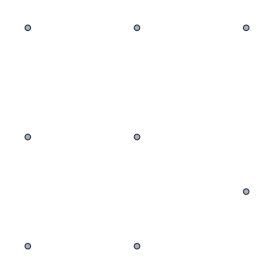

```mathematica
G
```

```mathematica
edges=EdgeList[G]
```

{}

## Bug: Copy-pasted Graph output looses edges

My guess is that this has something to do with how Graph[{..}, CompressedData[..]] appears to be used to store graphs in a notebook.

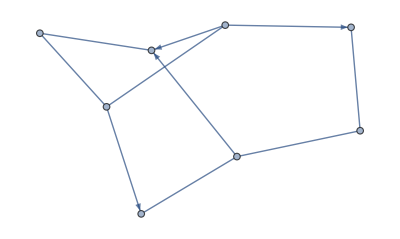
```mathematica
G=-Graphics-;
```

```mathematica
G
```

-Graphics-

```mathematica
GraphInformation[-Graphics-]
```

<|Acyclic→True,Bipartite→True,Complete→False,Connected→False,EdgeTransitive→True,WeightedEdge→False,Empty→True,Eulerian→True,Hamiltonian→False,LoopFree→True,Mixed→False,Path→False,Planar→True,Simple→True,Tree→False,Undirected→True,VertexTransitive→True,WeightedVertex→False,WeaklyConnected→False,Weighted→False|>

### Trying to store the graph as a PersistentSymbol value also looses the edges

Storing a graph to PersistentSymbol[“G”, “Notebook”] results in a graph missing all of it’s edges.

However, using the “Local” persistence location does preserve the edges.

It also appears that the types of the edges has an effect on whether the bug occurs or not. It seems that only mixed graphs exhibit the bug.

#### RandomGraph — works

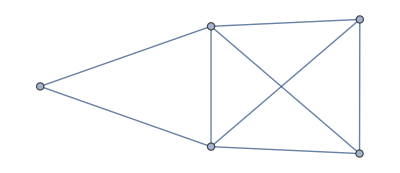

```mathematica
PersistentSymbol["G","Notebook"]=RandomGraph[{5,8}]
```

```mathematica
G=PersistentSymbol["G","Notebook"]
```

-Graphics-

#### RandomMixedGraph — doesn’t work

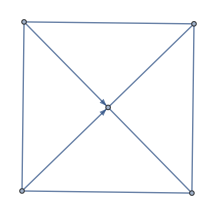

```mathematica
PersistentSymbol["G","Notebook"]=RandomMixedGraph[{5,8},0.25]
```

```mathematica
G=PersistentSymbol["G","Notebook"]
```

-Graphics-

## Scratch

```mathematica
G=RandomMixedGraph[{}]
```

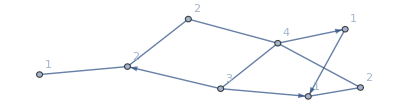

```mathematica
Graph[G,VertexLabels->Thread[VertexList[G]->VertexDegree[G]]]
```

```mathematica
edges=Graph[G,VertexLabels->"Name"]//EdgeList
```

{1->2,2->5,3->5,3->8,1<->3,1<->6,1<->7,4<->8,5<->6,7<->8}

```mathematica
namedEdges=edges//.n_Integer:>CharacterRange["A","Z"][[n]]
```

{A->B,B->E,C->E,C->H,A<->C,A<->F,A<->G,D<->H,E<->F,G<->H}

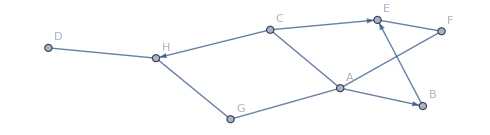

```mathematica
G4=Graph[namedEdges,VertexLabels->"Name"]
```

```mathematica
Thread[VertexList[G4]->VertexDegree[G4]]//Values//Sort
```

{1,2,2,2,3,3,3,4}

```mathematica
Thread[VertexList[G]->VertexDegree[G]]//Values//Sort
```

{1,1,1,2,2,2,3,4}

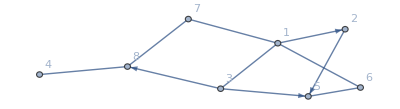

```mathematica
Graph[G,VertexLabels->"Name"]
```

```mathematica
VertexList[G]
```

{1,2,3,4,5,6,7,8}

```mathematica
VertexDegree[G]
```

{4,1,3,1,1,2,2,2}

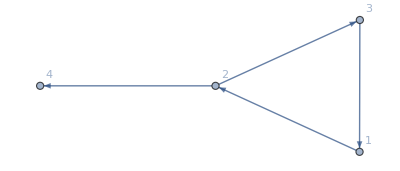

```mathematica
G2=Graph[{DirectedEdge[1, 2], DirectedEdge[2, 3], DirectedEdge[3, 1], 
  DirectedEdge[2, 4]},VertexLabels->"Name"]
```

```mathematica
VertexList[G2]
```

{1,2,3,4}

```mathematica
VertexDegree[G2]
```

{2,3,2,1}

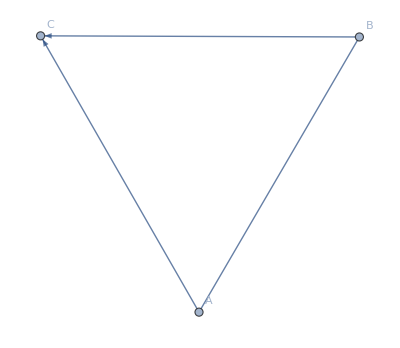

```mathematica
G3=Graph[{"A"<->"B","B"->"C","A"->"C"},VertexLabels->"Name"]
```

```mathematica
VertexList[G3]
```

{A,B,C}

```mathematica
VertexDegree[G3]
```

{2,2,2}

```mathematica
mixedGraph=Graph[{1<->2,2->3,3->1}];
FindEulerianCycle[mixedGraph]
```

FindEulerianCycle::ngen: The generalized FindEulerianCycle[Graph[<3>, <3>]] is not implemented.

FindEulerianCycle[-Graphics-]